```mathematica
b[v_,n_,t_]:=Binomial[n,v]t^v(1-t)^(n-v)
```

```mathematica
Plot3D[b[v,10,t],{v,0,10},{t,0,1}]
```

-Graphics3D-

```mathematica
Table[b[v,2,t],{v,0,2}]
```

{(1-t)^2,2 (1-t) t,t^2}

```mathematica
p[t_]:=4t^3-3t
```

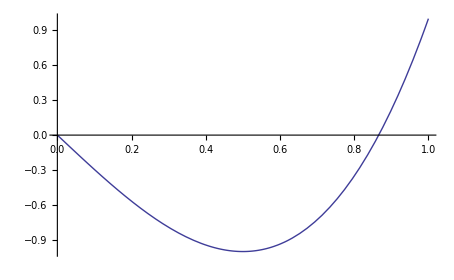

```mathematica
Plot[p[t],{t,0,1}]
```

```mathematica
a=({{2, 1, 0, 0, 0}, {1, 4, 1, 0, 0}, {0, 1, 4, 1, 0}, {0, 0, 1, 4, 1}, {0, 0, 0, 1, 2}})
```

{{2,1,0,0,0},{1,4,1,0,0},{0,1,4,1,0},{0,0,1,4,1},{0,0,0,1,2}}

```mathematica
b=({{d0}, {d1}, {d2}, {d3}, {d4}})
```

{{d0},{d1},{d2},{d3},{d4}}

```mathematica
c=6({{0}, {1/4}, {1}, {1/4}, {0}})
```

{{0},{3/2},{6},{3/2},{0}}

```mathematica
Solve[a.b==c]
```

{{d0→0,d1→0,d2→3/2,d3→0,d4→0}}

```mathematica
a=({{2, 1, 0, 0, 0}, {1, 4, 1, 0, 0}, {0, 1, 4, 1, 0}, {0, 0, 1, 4, 1}, {0, 0, 0, 1, 2}})
```

{{2,1,0,0,0},{1,4,1,0,0},{0,1,4,1,0},{0,0,1,4,1},{0,0,0,1,2}}

```mathematica
c=({{2}, {6}, {6(√5-1)}, {6}, {2}})
```

{{2},{6},{6 (-1+√5)},{6},{2}}

```mathematica
Solve[a.b==c]
```

{{d0→-1/12+(√5)/4,d1→13/6-(√5)/2,d2→-31/12+(7 √5)/4,d3→13/6-(√5)/2,d4→1/12 (-1+3 √5)}}

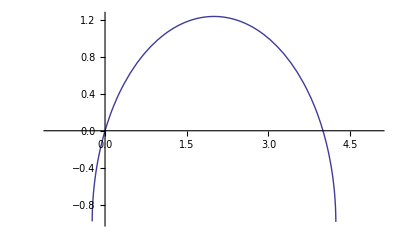

```mathematica
Plot[√(5-(x-2)^2)-1,{x,-1,5}]
```

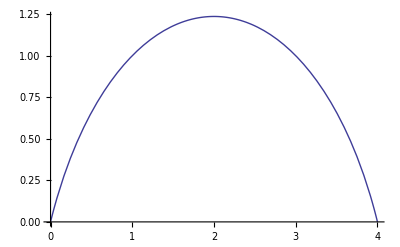

```mathematica
Plot[√(5-(x-2)^2)-1,{x,0,4}]
```

```mathematica
pts={{0,-1/12+(√5)/4},{1,13/6-(√5)/2},{2,-31/12+(7 √5)/4},{3,13/6-(√5)/2},{4,1/12 (-1+3 √5)},{5,13/6-√5/2},{-1,13/6-√5/2}}
```

{{0,-1/12+(√5)/4},{1,13/6-(√5)/2},{2,-31/12+(7 √5)/4},{3,13/6-(√5)/2},{4,1/12 (-1+3 √5)},{5,13/6-(√5)/2},{-1,13/6-(√5)/2}}

```mathematica
f=BSplineFunction[pts]
```

BSplineFunction[{{0.,1.}},<>]

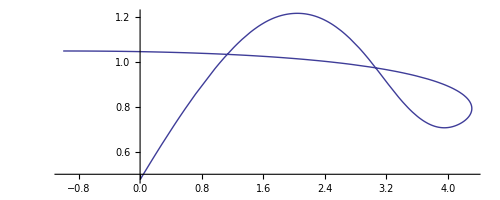

```mathematica
ParametricPlot[f[t],{t,-1,5}]
```

```mathematica
Expand[b0(1-t)^4+b1(4t(1-t)^3)+b2(6t^2(1-t)^2)+b3(4t^3(1-t))+b4(t^4)]
```

b0-4 b0 t+4 b1 t+6 b0 t^2-12 b1 t^2+6 b2 t^2-4 b0 t^3+12 b1 t^3-12 b2 t^3+4 b3 t^3+b0 t^4-4 b1 t^4+6 b2 t^4-4 b3 t^4+b4 t^4

```mathematica
%//FullSimplify
```

b0 (-1+t)^4+t (-4 b1 (-1+t)^3+t (6 b2 (-1+t)^2+t (4 b3-4 b3 t+b4 t)))

```mathematica
?Solve
```

RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to solve the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["dom", "TI"]}], "]"}] solves over the domain StyleBox["dom", "TI"]. Common choices of StyleBox["dom", "TI"] are Reals, Integers, and Complexes.

```mathematica
Solve[32+4b1==-1,b1]
```

{{b1→-33/4}}

```mathematica
-12*(-33/4)
```

99

```mathematica
Solve[-48-12(-33/4)+6b2==2,b2]
```

{{b2→-49/6}}

```mathematica
Solve[32+12(-33/4)-12(-49/6)+4b3==-2,b3]
```

{{b3→-33/4}}

```mathematica
Solve[-8-4(-33/4)+6(-49/6)-4(-33/4)+b4==4,b4]
```

{{b4→-5}}

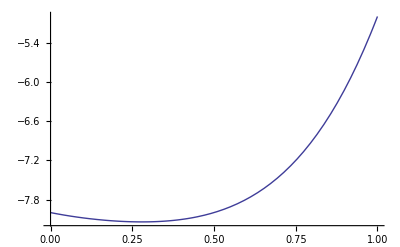

```mathematica
Plot[4x^4-2x^3+2x^2-x-8,{x,0,1}]
```

```mathematica
1/2(-8)+1/2(-33/4)
```

-65/8

```mathematica
1/2(-33/4)+1/2(149/6)
```

199/24

```mathematica
1/2(149/6)+1/2(363/4)
```

1387/24

```mathematica
1/2(363/4)+1/2(259)
```

1399/8

```mathematica
1/2(-65/8)+1/2(199/24)
```

1/12

```mathematica
1/2(199/24)+1/2(1387/24)
```

793/24

```mathematica
1/2(1387/24)+1/2(1399/24)
```

1393/24

```mathematica
1/2(1/12)+1/2(793/24)
```

265/16

```mathematica
1/2(793/24)+1/2(1393/24)
```

1093/24

```mathematica
1/2(265/16)+1/2(1093/24)
```

2981/96

```mathematica
p[x_]:=4x^4-2x^3+2x^2-x-8
```

```mathematica
p[1/2]
```

-8

```mathematica
2981/96//N
```

31.0521

```mathematica
a=1/6({{-3, 0, 3, 0, 0}, {1, 4, 1, 0, 0}, {0, 1, 4, 1, 0}, {0, 0, 1, 4, 1}, {0, 0, -3, 0, 3}})
```

{{-1/2,0,1/2,0,0},{1/6,2/3,1/6,0,0},{0,1/6,2/3,1/6,0},{0,0,1/6,2/3,1/6},{0,0,-1/2,0,1/2}}

```mathematica
b=({{d0}, {d1}, {d2}, {d3}, {d4}})
```

{{d0},{d1},{d2},{d3},{d4}}

```mathematica
c=({{-1}, {3}, {1}, {0}, {0}})
```

{{-1},{3},{1},{0},{0}}

```mathematica
Solve[a.b==c]
```

{{d0→8/3,d2→2/3,d1→11/3,d3→-1/3,d4→2/3}}

```mathematica
2/3-1/6
```

1/2

```mathematica
1/2*2/3+1/6*2/3+1/4*2/3
```

11/18

```mathematica
2*1/36+2*11/18
```

23/18

```mathematica
Integrate[-1+√(5-(x-2)^2),{x,0,4}]
```

-2+5 ArcSin[2/(√5)]

```mathematica
TrigToExp[%]
```

-2-5 ⅈ Log[(1+2 ⅈ)/(√5)]

```mathematica
%//N
```

3.53574

```mathematica
4*1/24(-t+3)^3+4(-1/6)(-2-t)^3+4*1/4(-1-t)^3+4*(-1/6)(-t)^3+4*1/24(1-t)^3
```

-2/3 (-2-t)^3+(-1-t)^3+1/6 (1-t)^3+1/6 (3-t)^3+(2 t^3)/3

```mathematica
%//Simplify
```

3 (3+t^2)

```mathematica
4*1/24(-t)^3+4(-1/6)(1-t)^3+4*1/4(2-t)^3+4*(-1/6)(3-t)^3+4*1/24(4-t)^3
```

-2/3 (1-t)^3+(2-t)^3-2/3 (3-t)^3+1/6 (4-t)^3-t^3/6

```mathematica
%//Simplify
```

0

```mathematica
4*1/24(0-t-4)^3+4(-1/6)(1-t-4)^3+4*1/4(2-t-4)^3+4*(-1/6)(3-t-4)^3+4*1/24(4-t-4)^3
```

1/6 (-4-t)^3-2/3 (-3-t)^3+(-2-t)^3-2/3 (-1-t)^3-t^3/6

```mathematica
%//Simplify
```

0

```mathematica
4*1/24(0-t-3)^3+4(-1/6)(1-t-3)^3+4*1/4(2-t-3)^3+4*(-1/6)(3-t-3)^3+4*1/24(4-t-3)^3
```

1/6 (-3-t)^3-2/3 (-2-t)^3+(-1-t)^3+1/6 (1-t)^3+(2 t^3)/3

```mathematica
%//Simplify
```

0

```mathematica
Integrate[0,t]
```

0

```mathematica
4*1/24(-2-t-3)^3+4(-1/6)(-1-t-3)^3+4*1/4(0-t-3)^3+4*(-1/6)(1-t-3)^3+4*1/24(2-t-3)^3
```

1/6 (-5-t)^3-2/3 (-4-t)^3+(-3-t)^3-2/3 (-2-t)^3+1/6 (-1-t)^3

```mathematica
%//Simplify
```

0

```mathematica
Integrate[4*1/24(0-t-3)^3,{t,0,1}]
```

-175/24

```mathematica
Integrate[4(-1/6)(1-t-3)^3,{t,0,1}]
```

65/6

```mathematica
Integrate[4*1/24(0-t-3)^3+4(-1/6)(1-t-3)^3+4*1/4(2-t-3)^3+4*(-1/6)(3-t-3)^3+4*1/24(4-t-3)^3,{t,0,1}]
```

0

```mathematica
Integrate[4*1/24(4-t-3)^3,{t,0,1}]
```

1/24

```mathematica
pts={{-1,-11/6-√5/2},{0,√5/4-1/12},{1,13/6-√5/2},{2,7*√5/4-31/12},{3,13/6-√5/2},{4,√5/4-1/12},{5,-11/6-√5/2}}
```

{{-1,-11/6-(√5)/2},{0,-1/12+(√5)/4},{1,13/6-(√5)/2},{2,-31/12+(7 √5)/4},{3,13/6-(√5)/2},{4,-1/12+(√5)/4},{5,-11/6-(√5)/2}}

```mathematica
f=BSplineFunction[pts,SplineDegree->3]
```

BSplineFunction[{{0.,1.}},<>]

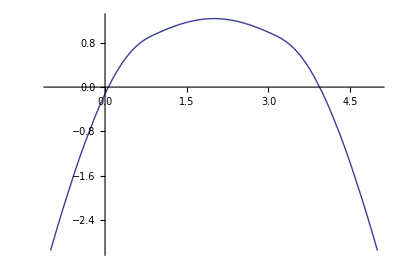

```mathematica
ParametricPlot[f[t],{t,0,4}]
```

```mathematica
Integrate[f[t],{t,0,4}]
```

∫_0^4 BSplineFunction[{{0.,1.}},<>][t]ⅆt

```mathematica
Integrate[InterpolatingFunction[pts[t]],{t,0,4}]
```

∫_0^4 InterpolatingFunction[{{-1,-11/6-(√5)/2},{0,-1/12+(√5)/4},{1,13/6-(√5)/2},{2,-31/12+(7 √5)/4},{3,13/6-(√5)/2},{4,-1/12+(√5)/4},{5,-11/6-(√5)/2}}[t]]ⅆt

```mathematica
ifun=Interpolation[pts]
```

InterpolatingFunction[{{-1,5}},<>]

```mathematica
Integrate[ifun[x],{x,0,4}]
```

47/12+(√5)/4+1/4 (19/4-(9 √5)/4+1/3 (9/4-(3 √5)/4))+1/8 (-19/4+(9 √5)/4+1/3 (-9/4+(3 √5)/4))+1/8 (9/4-(3 √5)/4+1/3 (3/4-(9 √5)/4)+1/2 (5/2-(3 √5)/2)+1/2 (-5/2+(3 √5)/2))+1/8 (19/4-(9 √5)/4+1/2 (5/2-(3 √5)/2)+1/3 (9/4-(3 √5)/4)+1/2 (-5/2+(3 √5)/2))+1/4 (1/2 (1/2-(3 √5)/2)+1/2 (7/4+(3 √5)/4+1/3 (3/4-(9 √5)/4)))+1/3 (19/4-(9 √5)/4+1/2 (19/4-(9 √5)/4+1/3 (9/4-(3 √5)/4))+1/2 (-19/4+(9 √5)/4+1/3 (-9/4+(3 √5)/4)))+1/2 (1/2 (-5/2+(3 √5)/2)+1/2 (-19/4+(9 √5)/4+1/2 (5/2-(3 √5)/2)+1/3 (-9/4+(3 √5)/4)+1/2 (-5/2+(3 √5)/2)))+1/3 (-19/4+(9 √5)/4+1/2 (5/2-(3 √5)/2)+1/2 (19/4-(9 √5)/4+1/2 (5/2-(3 √5)/2)+1/3 (9/4-(3 √5)/4)+1/2 (-5/2+(3 √5)/2))+1/2 (-19/4+(9 √5)/4+1/2 (5/2-(3 √5)/2)+1/3 (-9/4+(3 √5)/4)+1/2 (-5/2+(3 √5)/2)))+1/2 (1/2 (5/2-(3 √5)/2)+1/2 (-9/4+(3 √5)/4+1/2 (5/2-(3 √5)/2)+1/2 (-5/2+(3 √5)/2)+1/3 (-3/4+(9 √5)/4)))+1/3 (-9/4+(3 √5)/4+1/2 (-5/2+(3 √5)/2)+1/2 (9/4-(3 √5)/4+1/3 (3/4-(9 √5)/4)+1/2 (5/2-(3 √5)/2)+1/2 (-5/2+(3 √5)/2))+1/2 (-9/4+(3 √5)/4+1/2 (5/2-(3 √5)/2)+1/2 (-5/2+(3 √5)/2)+1/3 (-3/4+(9 √5)/4)))+1/3 (1/2 (1/2-(3 √5)/2)+1/2 (-1/2+(3 √5)/2)+1/2 (-7/4-(3 √5)/4+1/3 (-3/4+(9 √5)/4))-2 (1/2 (1/2-(3 √5)/2)+1/2 (7/4+(3 √5)/4+1/3 (3/4-(9 √5)/4))))+1/2 (-9/4+(3 √5)/4+1/2 (-1/2+(3 √5)/2)+2 (1/2 (1/2-(3 √5)/2)+1/2 (7/4+(3 √5)/4+1/3 (3/4-(9 √5)/4))))

```mathematica
%//FullSimplify
```

2+√5

```mathematica
%//N
```

4.23607

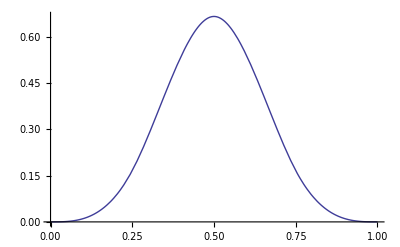

```mathematica
Plot[BSplineBasis[3,x],{x,0,1}]
```

```mathematica
BSplineBasis[{3,{0,1,2,3,4}},5,1]
```

BSplineBasis::invidx2: Index 5 should be a machine-sized integer between 0 and 0.

BSplineBasis[{3,{0,1,2,3,4}},5,1]

```mathematica
a1pts={{0,-8},{1/4,-33/4},{2/4,-49/6},{3/4,-33/4},{1,-5}}
```

{{0,-8},{1/4,-33/4},{1/2,-49/6},{3/4,-33/4},{1,-5}}

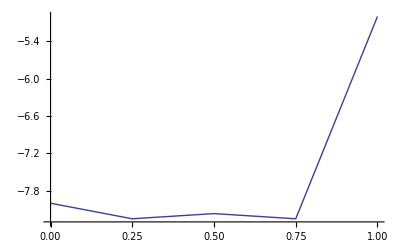

```mathematica
ListLinePlot[a1pts]
```

```mathematica
Plot[4x^4-2x^3+2x^2-x-8,{x,0,1}]
```

-Graphics-

```mathematica
f=BezierFunction[a1pts]
```

BezierFunction[{{0.,1.}},<>]

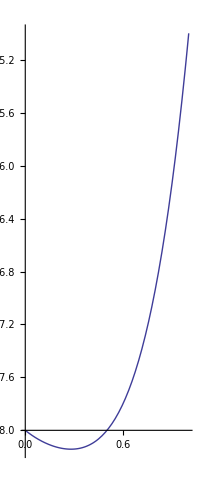

```mathematica
ParametricPlot[f[x],{x,0,1}]
```

```mathematica
1/2(-8)+1/2(-33/4)
```

-65/8

```mathematica
1/2(-33/4)+1/2(-49/6)
```

-197/24

```mathematica
1/2(-49/6)+1/2(-33/4)
```

-197/24

```mathematica
1/2(-33/4)+1/2(-5)
```

-53/8

```mathematica
1/2(-65/8)+1/2(-197/24)
```

-49/6

```mathematica
1/2(-197/24)+1/2(-197/24)
```

-197/24

```mathematica
1/2(-197/24)+1/2(-53/8)
```

-89/12

```mathematica
1/2(-65/8)+1/2(-49/6)
```

-391/48

```mathematica
1/2(-49/6)+1/2(-197/24)
```

-131/16

```mathematica
1/2(-197/24)+1/2(-89/12)
```

-125/16

```mathematica
1/2(-125/16)+1/2(-131/16)
```

-8

```mathematica
1/2(1/48)+1/2(19/48)
```

5/24

```mathematica
1/2(-65/16)+1/2(5/24)
```

-185/96

```mathematica
f[x_,v_]:=Piecewise[{{x-2v+1, 2v-1≤x<2v}, {-x+2v+1, 2v≤x<2v+1}}]
```

SetDelayed::write: Tag BezierFunction in TagBox[BezierFunction[1, {{0.`, 1.`}}, {4}, {{{0.`, -8.`}, {0.25`, -8.25`}, {0.5`, -8.166666666666666`}, {0.75`, -8.25`}, {1.`, -5.`}}, {}}, {0}, MachinePrecision,  is Protected.

$Failed